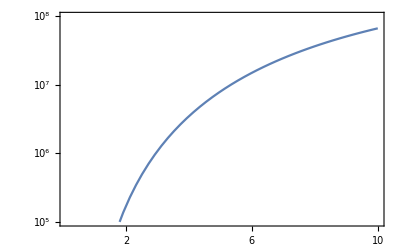

```mathematica
AME=0.5110034;
md=3670.481*AME;
mt=5496.918*AME;
μ=md mt/(md+mt);(*MeV/c^2*)
(*k=8.617333262*10^(-11);*)
k=1;
eh=1/137;
coefficient=(2 Sqrt[2])/(Sqrt[π k μ]*k);
change=1.807*10^10;
η[en_]:=eh*Sqrt[μ/(2*en)];
S[en_]:=(26-0.361*en+248*en^2)/(1+((en-0.0479)/0.0392)^2);
efactor[T_,en_]:=Exp[-en/(k*T)-2π*η[en]];
pro[T_]:=change*coefficient*T^(-3/2)*NIntegrate[S[x]*efactor[T,x],{x,0,0.3}];
Plot[pro[10^-3*T],{T,0.1,10},ScalingFunctions->{"Linear","Log"},(*纵轴对数坐标*)Frame->True,PlotRange->{Full,{10^5,10^8}}]
```

```mathematica
Export["/Users/LiZnB/Desktop/T.png",%240,"PNG"]
```

/Users/LiZnB/Desktop/T.png